# Hexi—PS19—2025 - 04 - 18

### Exercises from EIWL3 Section 44

```mathematica
Import["https://www.google.com","Images"]
```

{-Graphics-}

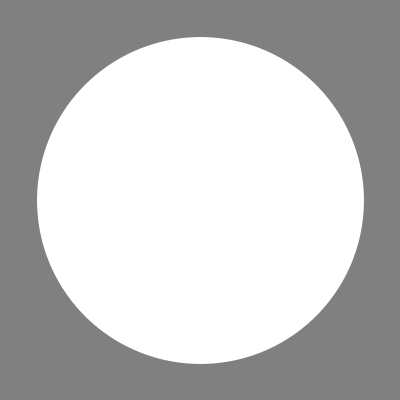
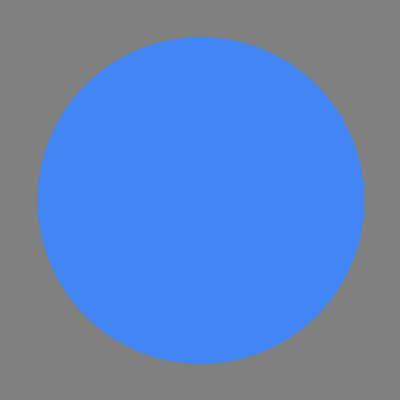
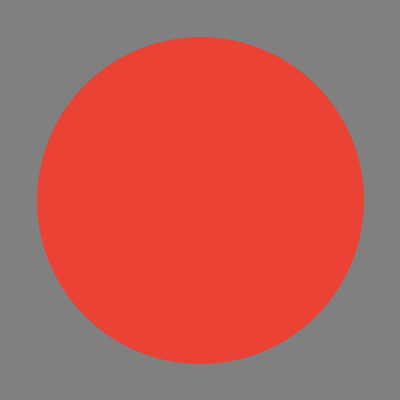
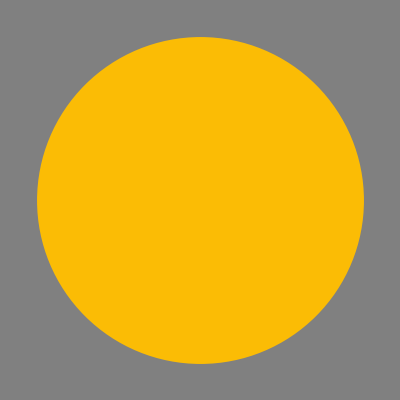
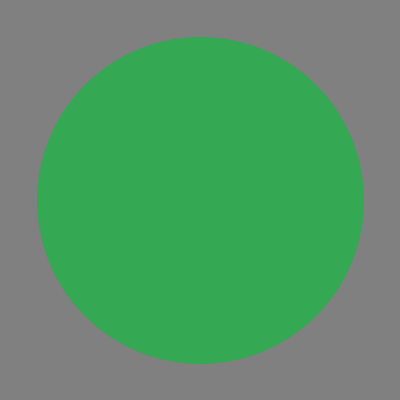

```mathematica
Graphics[{#,Disk[]},Background->Gray]&/@Flatten[DominantColors[Import["https://www.google.com","Images"]]]
```

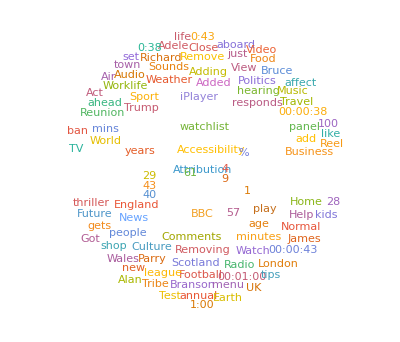

```mathematica
WordCloud[Import["https://bbc.co.uk."]]
```

```mathematica
ImageCollage[Import["https://nps.gov","Images"]]
```

-Graphics-

```mathematica
Select[Import["https://en.wikipedia.org/wiki/Ostrich","Images"],ImageInstanceQ[#,"bird"]&]
```

```mathematica
WordCloud[TextCases[Import["https://www.nato.int"],"Country"]]
```

```mathematica
Import["https://en.wikipedia.org","Hyperlinks"]//Length
```

362

```mathematica
SendMail["hexi.jinkx@deepsprings.edu",GeoGraphics[Here]]
```

SendMail::cloudrelay: SendMail has relayed your message through the Wolfram Cloud.  A local SMTP server has not been configured. These settings can be defined through Preferences > Internet & Mail > Mail Settings in the notebook front end.

Success[…]

```mathematica
SendMail["hexi.jinkx@deepsprings.edu",MoonPhase[Now,"Icon"]]
```

LibraryFunction::rterr: An error with return code 100 was encountered evaluating the function illumination_phase_angle.

Success[…]